```mathematica
file="/home/levesque/Recherche/src/autoCorrelation/tests/test4/original_files_by_Xudong/atom1";
```

```mathematica
data=Import[file,"Table"];//AbsoluteTiming
```

{2.22867,Null}

```mathematica
dim=Dimensions[data][[1]]
```

101662

```mathematica
Clear[matx,maty,matz,mat];
mat[i_]:=mat[i]=data[[All,i]]
```

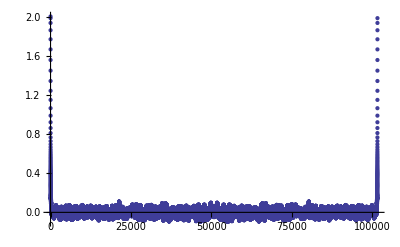

```mathematica
ListPlot[
InverseFourier[Fourier[mat[1]]Conjugate[Fourier[mat[1]]]],
PlotRange->Full
]
```

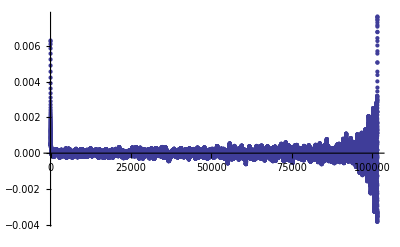

```mathematica
ListPlot[ListCorrelate[mat[1],mat[1],1,0]/Range[dim,1,-1],
PlotRange->Full]
```

```mathematica
ref=Import["/home/levesque/Recherche/src/autoCorrelation/tests/test4/original_files_by_Xudong/acf1.out","Table"];
```

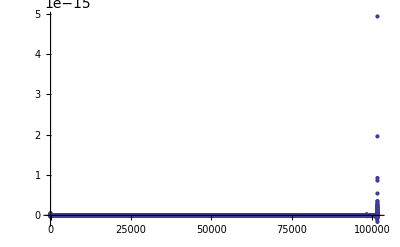

```mathematica
ListPlot[ref-
Sum[
ListCorrelate[mat[i],mat[i],1,0]
,{i,3}]/Range[dim,1,-1],
PlotRange->Full]
```

```mathematica
ref[[All,2]]-Sum[ListCorrelate[mat[i],mat[i],1,0],{i,3}]/Range[dim,1,-1]
```

{2.42861×10^-17,1.38778×10^-17,-3.46945×10^-17,2.77556×10^-17,3.1225×10^-17,«101652»,-1.40946×10^-17,8.63675×10^-16,5.41959×10^-16,1.95926×10^-15,4.93442×10^-15}

```mathematica
ref
```

{{0,0.0188058},{1,0.0186438},{2,0.0181825},{3,0.0174824},«101654»,{101658,0.000654148},{101659,-0.0000472764},{101660,-0.000849356},{101661,-0.00171564}}

```mathematica
Sum[ListCorrelate[mat[i],mat[i],1,0],{i,3}]/Range[dim,1,-1]
```

{0.0188058,0.0186438,0.0181825,0.0174824,0.0166141,«101652»,0.00118376,0.000654148,-0.0000472764,-0.000849356,-0.00171564}

Ma conclusion arrivé ici est que ce que je calcule brutalement est équivalent à un listconvolve renormalisé. On est obligé d’utiliser du zeropadding pour ne pas faire de cyclic correlation.